# Lab 3: Derivatives, Manipulates

## Kyle Perra - 7/9/2015

## Mathematica Fundamentals

```mathematica
N[2 +3]
```

5.

```mathematica
√2
```

√2

```mathematica
N[√2]
```

1.41421

```mathematica
√2* 3
```

```mathematica
N[3 √5]
```

6.7082

```mathematica
N[3 √2]
```

4.24264

```mathematica
N[3/17*12 - 77]
```

-74.8824

```mathematica
3/17*12-77
```

-1273/17

```mathematica
N[(12-43*√(3/4+4))/17]
```

-4.80684

```mathematica
N[√3*(√3)/5]
```

0.6

```mathematica
N[√(17/(√(.05)))*-78]
```

-680.106

```mathematica
N[√((12-(3 √7)/4+17)/22)]
```

1.10815

```mathematica
y[x_] := -12x^2+15x+7
```

```mathematica
y[2]
y'[2]
```

-11

-33

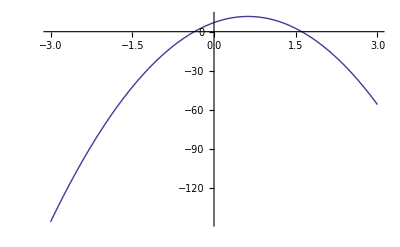

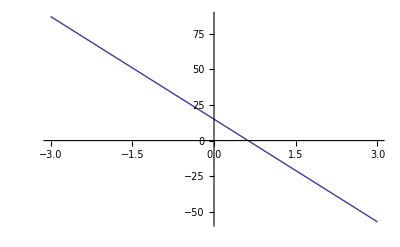

```mathematica
Plot[y[x],{x,-3,3}]
Plot[y'[x],{x,-3,3}]
```

## Interpretation of Plot

```mathematica
The derivative of y(x) [NOT f(x), as noted in the lab assignment instruction sheet] is equal to zero at approx. x= .6
This shows us that the behavior in the upper plot dictates the display of the second plot; ultimately the derivative (second plot) shows the slope of the function y(x) at a given x value.
```

## Manipulate - Functions

```mathematica
Manipulate[x,{x,1,15}]
```

```mathematica
Manipulate[x,{x,1,15,1}]
```

```mathematica
Manipulate[x*y,{x,-2,5,1},{y,1.5,16}]
```

```mathematica
Manipulate[x*y,{x,-2,5,1,Appearance->"Labeled"},{y,1.5,16,Appearance->"Labeled"}]
```

```mathematica
Manipulate[x*Factorial[y],{x,1,100000,1,Appearance->"Labeled"},{y,1,30,1,Appearance->"Labeled"}]
```

## Manipulate - Plots

```mathematica
f[x_,z_]:=-x^z+15x
```

```mathematica
Manipulate[Plot[f[x,z],{x,-15,15}],{z,1,10,1,Apperance->"Labeled"}]
```